```mathematica
Get["sac.m",Path->NotebookDirectory[]];
```

```mathematica
?sac`*
```

```mathematica
history=Simulate[500,50000];
```

```mathematica
effectiveHistory=Take[history,-40000];
```

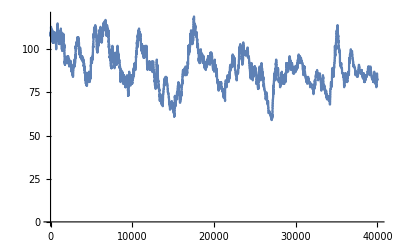

```mathematica
ListPlot[Unemployed[effectiveHistory],Joined->True,PlotRange->All]
```

```mathematica
firmHistories=FirmHistories[effectiveHistory];
```

```mathematica
firmProfitRates=FirmProfitRates[firmHistories];
```

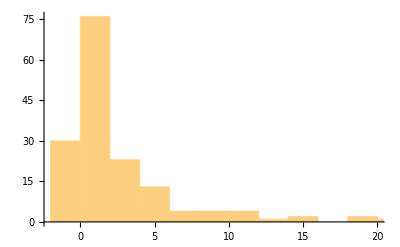
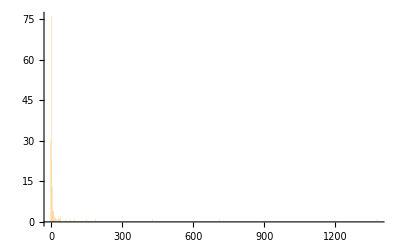

```mathematica
{Histogram[firmProfitRates],Histogram[firmProfitRates,PlotRange->All]}
```

```mathematica
firmSizes=FirmSizes[effectiveHistory];
```

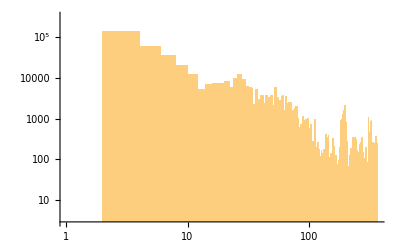

```mathematica
(* Should be a straight line *)
Histogram[firmSizes,PlotRange->All,ScalingFunctions->{"Log","Log"}]
```

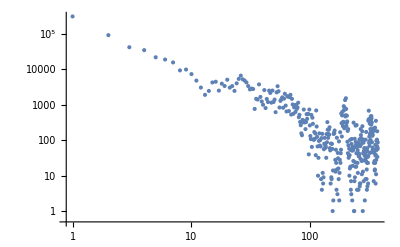

```mathematica
(* Should be a straight line *)
ListPlot[Drop[BinCounts[firmSizes],1],ScalingFunctions->{"Log","Log"},PlotRange->All]
```

```mathematica
EstimatedDistribution[firmSizes,ZipfDistribution[a,b]]
```

ZipfDistribution[369,0.4257]

```mathematica
firmSizesSample=RandomSample[firmSizes,Round[Length[firmSizes]*0.01]];
```

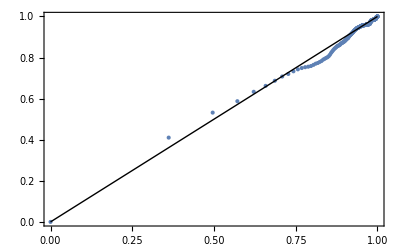

```mathematica
ProbabilityPlot[firmSizesSample,ZipfDistribution[a,b],PlotRange->All]
```

```mathematica
workersMoney=EmployeesMoney[effectiveHistory];
```

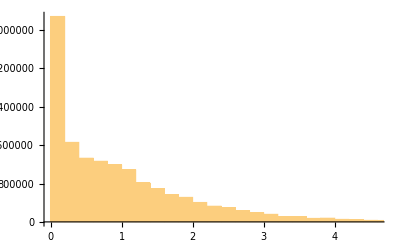

```mathematica
Histogram[workersMoney]
```

```mathematica
workersMoneySample=RandomSample[workersMoney,Round[Length[workersMoney]*0.01]];
```

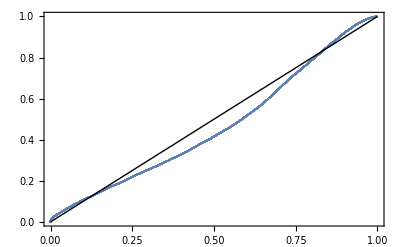

```mathematica
ProbabilityPlot[workersMoneySample,GammaDistribution[a,b]]
```

```mathematica
FindDistribution[workersMoneySample,TargetFunctions->"Continuous",MaxItems->3,PerformanceGoal->"Quality"]
```

MixtureDistribution[{0.792934,0.207066},{GammaDistribution[0.288575,2.49877],LogNormalDistribution[0.397241,0.494812]}]

```mathematica
employersWealth=EmployersWealth[effectiveHistory];
```

```mathematica
employersWealthSample=RandomSample[employersWealth,Round[Length[employersWealth]*0.01]];
```

```mathematica
(* N.B. c=0 means location parameter is inoperative, and so reduces to ParetoDistribution[a,b] *)
EstimatedDistribution[employersWealthSample,ParetoDistribution[a,b,d]]
```

ParetoDistribution[13.8804,1.73224,0.00041091]

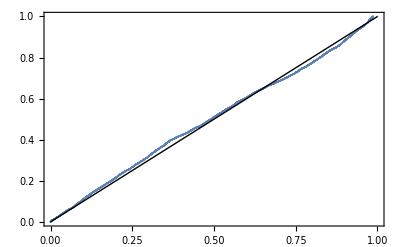

```mathematica
ProbabilityPlot[employersWealthSample,ParetoDistribution[a,b,d]]
```